# “Hump-backed plateau”

Make sure you set the pathpackage below to your current package directory

```mathematica
pathpackage="/Users/gianmicheleinnocenti/Desktop/parton-shower-simulator";
Clear[kernelpath,notebookpath];
kernelpath = StringJoin[pathpackage,"/Kernel"];
resultspath = StringJoin[pathpackage,"/Notebooks/plots"];
pathmain = StringJoin[kernelpath,"/PartonShowerMCFull.wl"]
SetDirectory[kernelpath];
<<"PartonShowerMCFull.wl"
SilentErrors[];
SetStandardSeeds[];
```

/Users/gianmicheleinnocenti/Desktop/parton-shower-simulator/Kernel/PartonShowerMCFull.wl

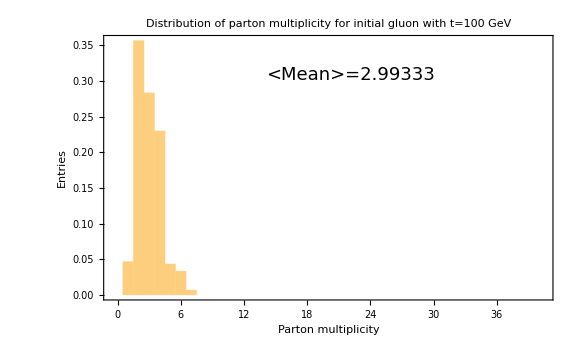
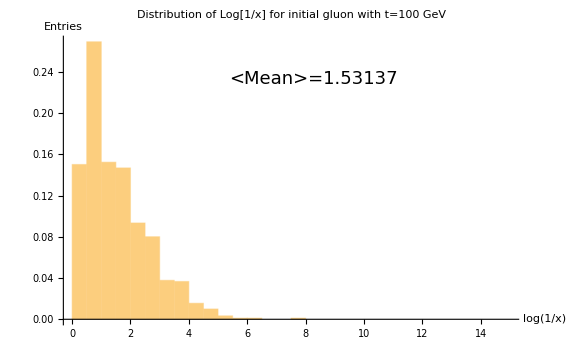
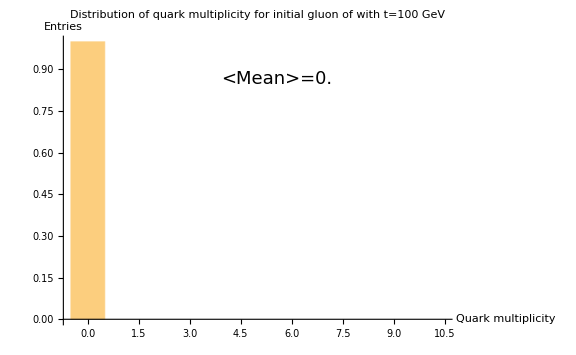
/Users/gianmicheleinnocenti/Desktop/parton-shower-simulator/Notebooks/plots/plotsNTonlygtogg_histolog1overz_maxevents300_tscalecutoff1.0_scale100GeVc.pdf /Users/gianmicheleinnocenti/Desktop/parton-shower-simulator/Notebooks/plots/plotsNTonlygtogg_histomultinit_maxevents300_tscalecutoff1.0_scale100GeVc.pdf /Users/gianmicheleinnocenti/Desktop/parton-shower-simulator/Notebooks/plots/plotsNTonlygtogg_histonquarks_maxevents300_tscalecutoff1.0_scale100GeVc.pdf -Graphics- -Graphics- -Graphics-

```mathematica
SetStandardSeeds[];
resultspath = StringJoin[pathpackage,"/Notebooks/plots/plotsNTonlygtogg_"];
RunShowerMulti[1000,100,1.,SudakovPgtoggvacuumNT,SudakovPgtoqqbarvacuumLT,PgtoggvacuumNT,PgtoqqbarvacuumLT,PgtoggvacuumNTsymmetric,0,200,0,resultspath]
```

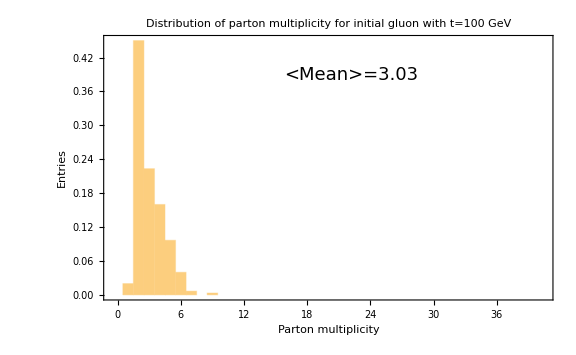
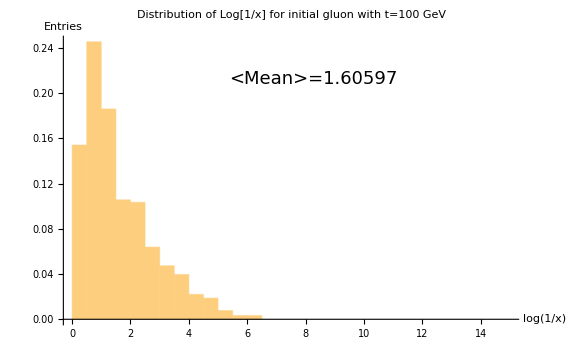
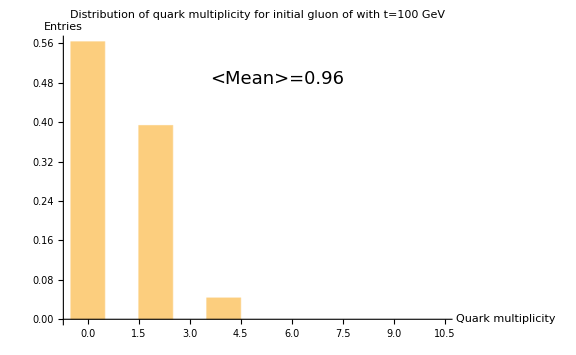
/Users/gianmicheleinnocenti/Desktop/parton-shower-simulator/Notebooks/plots/plotsNTonlygtogg_histolog1overz_maxevents300_tscalecutoff1.0_scale100GeVc.pdf /Users/gianmicheleinnocenti/Desktop/parton-shower-simulator/Notebooks/plots/plotsNTonlygtogg_histomultinit_maxevents300_tscalecutoff1.0_scale100GeVc.pdf /Users/gianmicheleinnocenti/Desktop/parton-shower-simulator/Notebooks/plots/plotsNTonlygtogg_histonquarks_maxevents300_tscalecutoff1.0_scale100GeVc.pdf -Graphics- -Graphics- -Graphics-

```mathematica
SetStandardSeeds[];
resultspath = StringJoin[pathpackage,"/Notebooks/plots/plotsNTonlygtogg_"];
RunShowerMulti[1000,100,1.,SudakovPgtoggvacuumNT,SudakovPgtoqqbarvacuumLT,PgtoggvacuumNT,PgtoqqbarvacuumLT,PgtoggvacuumNTsymmetric,0,200,1,resultspath]
```

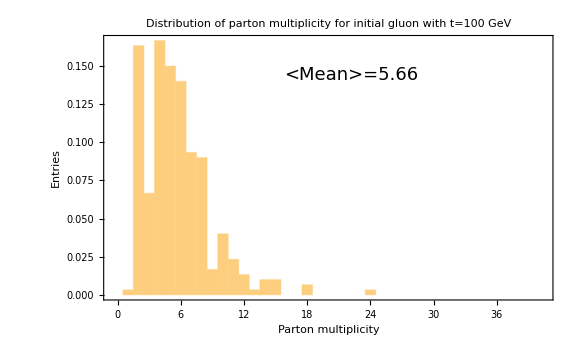
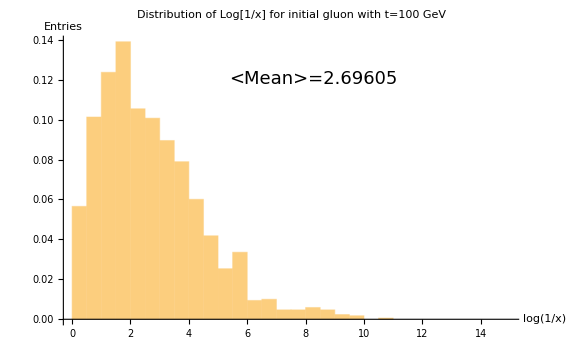
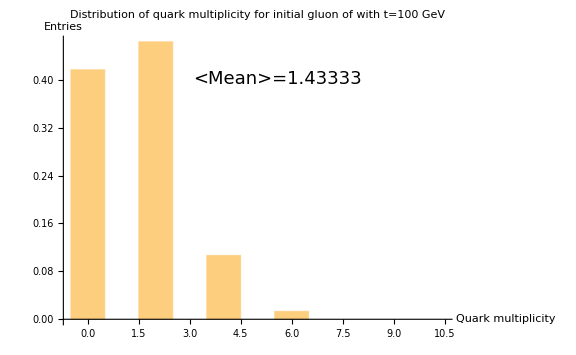
/Users/gianmicheleinnocenti/Desktop/parton-shower-simulator/Notebooks/plots/plotsNTonlygtogg_histolog1overz_maxevents300_tscalecutoff1.0_scale100GeVc.pdf /Users/gianmicheleinnocenti/Desktop/parton-shower-simulator/Notebooks/plots/plotsNTonlygtogg_histomultinit_maxevents300_tscalecutoff1.0_scale100GeVc.pdf /Users/gianmicheleinnocenti/Desktop/parton-shower-simulator/Notebooks/plots/plotsNTonlygtogg_histonquarks_maxevents300_tscalecutoff1.0_scale100GeVc.pdf -Graphics- -Graphics- -Graphics-

```mathematica
SetStandardSeeds[];
resultspath = StringJoin[pathpackage,"/Notebooks/plots/plotsNTonlygtogg_"];
RunShowerMulti[1000,100,1.,SudakovPgtoggvacuumNTQ2Medium,SudakovPgtoqqbarvacuumLT,PgtoggvacuumNT,PgtoqqbarvacuumLT,PgtoggvacuumNTsymmetric,0,200,1,resultspath]
```